```mathematica
SetDirectory[NotebookDirectory[]];
vmax=20;
rBar=4;
Lf=vmax*Max[1,1/rBar^2+1/rBar];
sigma=0.48;
lr=2;
Lh=1/rBar^2;
rmin[xi_,off_]:=rBar/(sigma*Cos[xi/2]+1-sigma)+off;
h[xi_,off_]:=(sigma*Cos[xi/2]+1-sigma)/rBar-1/rmin[xi,off];
f[xi_,beta_,off_]:={vmax*Cos[xi-beta],-vmax/rmin[xi,off]*Sin[xi-beta]-vmax/lr*Sin[beta]};
deltaFMax=Pi/4;
betaMax=ArcTan[0.5*Tan[deltaFMax]];
```

## Solution for Cloud Wait Time (aka “Δt”)

Recall from our prior calculations that we are interested in solutions for t of the following equation:

Sqrt[2]*Lh*Norm[f[ξ, β0, offset]]*t*Exp[Lf*t] == h[ξ, offset]

This equation can be solved numerically to any desired accuracy for any particular choice of ξ and β_0 (and offset although we will focus on the others -- see note below); however, we need to be able to determine a wait-time value for any possible (real-valued) values for ξ and β_0. Thus, we use analytical information about the functions (equation) in question to construct a lookup table whose elements are spaced finely enough that we can bound the difference between any real-valued (ξ,β_0) and the nearest point stored in the lookup table.

Note: we have parameterized this equation by r_min[ξ]+offset for the usual technical reasons. In particular, the value of h[ξ,r_min[ξ]+offset] increases in the variable offset for each ξ (I believe this needs to be shown still -- the analogous result in the paper is for the more complicated ZBF).

## Using the Implicit Function Theorem to Bound the Derivative of the Solution of (1)

The obvious approach to determine a grid size for the lookup table is to bound the Lipschitz constant of the function in question. In particular, we will consider that (1) defines an implicit function of ξ and β_0 for each value of offset. We denote this function by:

t̃:(ξ,β_0)∈[-π,π]×[-β_max,β_max]→ℝ

i.e. t̃[ξ,β_0] solves (1) above. Define the following set for convenience:

D=[-π,π]×[-β_max,β_max]

We can rewrite (1) as an equation with zero as a right-hand side, and specify this in Mathematica as follows:

```mathematica
F=Evaluate[Sqrt[2]*Lh*Norm[f[ξ,β0,offset]]*t*Exp[Lf*t]-h[ξ,offset]]
```

(ⅇ^(20 t) t √(400 Abs[Cos[β0-ξ]]^2+Abs[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2))/(8 √2)+1/(offset+4/(0.52+0.48 Cos[ξ/2]))+1/4 (-0.52-0.48 Cos[ξ/2])

Now the implicit function theorem says (in part) that the gradient of t̃[ξ,β_0] with respect to (ξ,β_0) can be expressed in terms of the implicit function, t̃:

(∂t̃)/(∂(ξ,β_0))[ξ,β_0]=-((∂F)/(∂t)[ξ,β_0,t̃[ξ,β_0]])^-1*(∂F)/(∂(ξ,β_0))[ξ,β_0,t̃[ξ,β_0]]

provided the gradient ∂F/∂t is invertible. Since we are interested in bounding the Lipschitz constant of t̃, we can apply the Mean-Value Theorem (MVT) if we are able to bound the gradient in (3).

We can have Mathematica compute the appropriate expressions as follows. Let:

dF_den[ξ,β_0]=(∂F)/(∂t)[ξ,β_0,t̃[ξ,β_0]]
dF_num[ξ,β_0]=(∂F)/(∂(ξ,β_0))[ξ,β_0,t̃[ξ,β_0]]

then compute:

```mathematica
dFnum=D[F,{{ξ,β0}}]; (* Surpressed output for convenience *)
```

```mathematica
dFden=Simplify[D[F,t]]
```

(5 ⅇ^(20 t) (1+20 t) √(4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2))/(4 √2)

In particular, we can upper-bound the expression in (4) by upper-bounding the numerator, dF_num, and simultaneously lower-bounding the denominator, dF_den. The numerator is generally no problem; we skip that for later. Clearly, a lower bound for the denominator can be obtained by separately lower-bounding the two factors in the expression above. The first, ⅇ^(20 t) (1+20 t), is clearly lower-bounded by 1, since any solution for t of (1) is non-negative. Thus, we have to consider a lower bound for the other expression, extracted here:

```mathematica
lowerBoundQty[ξ_,β0_,offset_]:=Evaluate[Reap[Simplify[D[F,t]]/.Sqrt[x_]:>Sow[x]]⟦2⟧//Flatten//First]
lowerBoundQty[ξ,β0,offset]
```

4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2

(noting that √is monotonic, so can be omitted from determining the (ξ^*,β_0^*) of the minimum).

However, it is unfortunately the case that the minimum of lowerBoundQty[ξ,β0,offset] is zero on the region of interest (note the particular choice of offset 5):

```mathematica
offs=1;
```

```mathematica
badMin=FindMinimum[
lowerBoundQty[ξ,β0,offs],
{{ξ,-Pi/2},{β0,0}}
]
```

{4.28318×10^-28,{ξ→-1.1883,β0→0.382495}}

This is obviously unacceptable, since it creates a trivial lower-bound on dF_den of 0, and hence a trivial upper-bound on the quantity of ultimate interest, (∂t̃)/(∂(ξ,β_0))[ξ,β_0], viz. +∞.

Note: this means that there is NO finite grid-size over the ENTIRE REGION [-π,π]×[-β_max,β_max] that will create a finite upper-bound on the error between t̃[ξ,β_0] and any grid point!

## Bounding the denominator of Implicit Function Gradient (old method)

Thus, we take the following approach. We will split the set [-π,π]×[-β_max,β_max] into two subsets: one on which lowerBoundQty is bounded below by a small -- but finite -- value, and the other on which lowerBoundQty can reach zero, but on which every solution t̃[ξ,β_0] is larger than some fixed value. Formally, we wish to choose some set S_offset⊂[-π,π]×[-β_max,β_max]=D such that the following hold:

∀(ξ,β_0)∈D\S_offset . lowerBoundQty[ξ,β_0,offset]>=δ_offset

∀(ξ,β_0)∈S_offset . t̃[ξ,β_0,offset]>=T_offset

for some constants δ_offset and T_offset (functions of only offset).

One natural way to obtain such a set is to solve (1) using instead an upper-bound on its left-hand side. This will immediately give us a set of points (in the ξ-β_0 plane) for which (7) is true. In particular, let’s consider upper-bounding the t factor in (1) by Exp[t]. Thus, we can define a set S_offset as follows for a particular choice of T_offset:

S_offset={(ξ,β_0)∈D: 1/(2*Lf)*Log[h[ξ,offset]/(Sqrt[2]*Lh*Norm[f[ξ,β0,offset]])]>=T_max}

This choice comes with the assurance that ∀(ξ,β_0)∈S_offset. t̃[ξ,β_0]>=T_max. Thus, if we are lucky, we can prove that (6) holds for this set as well.

This seems likely to be the case, given the following observation. Consider the following plot, which shows the upper-bound expression used in (8) with the actual numerical solutions to (1). In particular, the output range of the plot is limited to [0,0.25], and the input range is set to a small interval around (one of) the points at which lowerBoundQty is zero, viz. {ξ→-1.53857,β0→0.0322252} from the numerical minimization above. (The orange surface is the numerical solution to (1); the blue surface is a plot of the expression in (8).)

```mathematica
Tmax[offs]=0.075
```

0.075

```mathematica
numPoints=40;
rng={{ξ-0.1,ξ+0.1},{β0-0.1,β0+0.1}}/.badMin⟦2⟧;
data=Flatten[ParallelTable[
{xi,beta,t/.Flatten@Quiet@NSolve[Sqrt[2]*2*Lh*Norm[f[xi,beta,offs]]*t*Exp[Lf*t]==h[xi,offs],t]},
{xi,rng⟦1,1⟧,rng⟦1,2⟧,(rng⟦1,2⟧-rng⟦1,1⟧)/numPoints},
{beta,rng⟦2,1⟧,rng⟦2,2⟧,(rng⟦2,2⟧-rng⟦2,1⟧)/(2*numPoints)}
],1];
Show[
ListPlot3D[
data,
AxesLabel->(Style[#,FontSize->16]&/@{"ξ","β","Δt"}),
PlotRange->{0,Tmax[offs]}
],
Plot3D[
Log[h[ξ,offs]/(Sqrt[2]*Lh*Norm[f[ξ,β0,offs]])]/(2*Lf),
{ξ,rng⟦1,1⟧,rng⟦1,2⟧},
{β0,rng⟦2,1⟧,rng⟦2,2⟧},
PlotRange->{0,0.25},
PlotPoints->50,
PlotTheme->"CoolColor",
PlotStyle->{Directive[Opacity[0.5]]}
],
PlotRange->{rng⟦1⟧,rng⟦2⟧,{0,Tmax[offs]}}
]
```

-Graphics3D-

-Graphics3D-

As expected, the blue surface is always less-than the orange one, so that the super-level set in (8) is guaranteed to be contained within the super-level set of the actual numerical solution to (1), viz. {(ξ,β_0):t̃[ξ,β_0]>=T_offset=0.25}. However, we note further that the solution of (1) for the problematic point of lowerBoundQty is well within this set:

```mathematica
FindMinimum[
Evaluate[F/.badMin⟦2⟧/.offset->offs]^2,
{{t,1}}
]
```

{2.55178×10^-29,{t→0.829205}}

This is clearly larger than the choice T_offset=0.2 for offset=5.

So it is very likely that (6) holds for this choice of S_offset for some finite value δ_offset.

This is the subject of the next subsection, although here we will do things a little bit sloppily (i.e. numerically).

### Finding a lower bound for the denominator on D\S_offset

We will proceed with this objective -- i.e. “proving” (6) holds for our choice of S_offset -- using numerical optimization on a Lagrangian. First, though, we should convince ourselves that the minima of the denominator appear only on the boundary of the set S_offset. For now, we will do this just by inspection since time is short.

```mathematica
Plot3D[
lowerBoundQty[ξ,β0,offs],
{ξ,rng⟦1,1⟧,rng⟦1,2⟧},
{β0,rng⟦2,1⟧,rng⟦2,2⟧},
PlotRange->{0,1}
]
```

-Graphics3D-

```mathematica
Plot3D[
lowerBoundQty[ξ,β0,offs],
{ξ,-Pi,Pi},
{β0,-Pi/4,Pi/4},
PlotRange->{0,5}
]
```

-Graphics3D-

```mathematica
optimPlotRange={{ξ-0.02,ξ+0.02},{β0-0.02,β0+0.02}}/.badMin⟦2⟧;
ListPlot3D[
Flatten[Table[
If[
(Log[h[ξ,offs]/(Sqrt[2]*Lh*Norm[f[ξ,β0,offs]])]/(2*Lf))>=Tmax[offs],
{ξ,β0,lowerBoundQty[ξ,β0,offs]},
{ξ,β0,0}
],
{ξ,optimPlotRange⟦1,1⟧,optimPlotRange⟦1,2⟧,(optimPlotRange⟦1,2⟧-optimPlotRange⟦1,1⟧)/250},
{β0,optimPlotRange⟦2,1⟧,optimPlotRange⟦2,2⟧,(optimPlotRange⟦2,2⟧-optimPlotRange⟦2,1⟧)/250}
],1],
PlotRange->{0,0.0001}
]
```

-Graphics3D-

```mathematica
Dimensions[%]
```

{2}

Together, these suggest that the minimum of lowerBoundQty over the set D\S_offset is indeed likely to be on the boundary of S_offset. Thus, we proceed under this assumption, and use a single Lagrange multiplier to account for this equality constraint, viz:

```mathematica
L[ξ_,β0_,offset_,λ_,Toff_]:=lowerBoundQty[ξ,β0,offset]+λ*(Sqrt[2]*Lh*Norm[f[ξ,β0,offset]]*ⅇ^(2*Lf*Toff)-h[ξ,offset])
constraint[ξ_,β0_,offset_,Toff_]:=Sqrt[2]*Lh*Norm[f[ξ,β0,offset]]*ⅇ^(2*Lf*Toff)-h[ξ,offset]
```

```mathematica
Norm[f[ξ,β0,offset]]
```

√(400 Abs[Cos[β0-ξ]]^2+Abs[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2)

```mathematica
lowerBoundQty[ξ,β0,offset]
```

4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2

In Mathematica, we proceed to take symbolic gradients, and then do numerical optimization with careful initialization to attempt to find a solution:

```mathematica
Remove[dL]
```

```mathematica
badMin
```

{1.01819×10^-16,{ξ→-1.35815,β0→0.212643}}

```mathematica
dL[ξ_,β0_,λ_]:=Evaluate[First[Norm[D[L[ξ,β0,offs,λ,Tmax[offs]],{{ξ,β0}}]]]^2/.Abs'->Sign];
optimRange={{ξ-0.5,ξ+0.5},{β0-0.5,β0+0.5}}/.badMin⟦2⟧;
TakeSmallestBy[(constraint[#⟦2,2,1,2⟧,#⟦2,2,2,2⟧,offs,Tmax[offs]]^2)&,5]@Flatten[
TakeSmallestBy[(constraint[#⟦2,2,1,2⟧,#⟦2,2,2,2⟧,offs,Tmax[offs]]^2)&,5]/@ParallelTable[
Quiet[
({lowerBoundQty[#⟦2,1,2⟧,#⟦2,2,2⟧,offs],#})&@FindMinimum[
dL[ξ,β0,λ],
{{ξ,ξ00},{β0,β00},{λ,0.2}},
PrecisionGoal->40,
AccuracyGoal->40,
WorkingPrecision->60,
MaxIterations->10000
]
],
{ξ00,optimRange⟦1,1⟧,optimRange⟦1,2⟧,(optimRange⟦1,2⟧-optimRange⟦1,1⟧)/100},
{β00,optimRange⟦2,1⟧,optimRange⟦2,2⟧,(optimRange⟦2,2⟧-optimRange⟦2,1⟧)/100}
],
1
]
```

{{0.0000431964,{1.60666294518167903243373783151933487405343314231370600748927×10^-22,{ξ→-1.36574418651997990669172226869820987744885832754459009671602,β0→0.206712093619491478025627582224061636010334634628779699874366,λ→-0.000739218082765785425630038460754000096789837067247845567003154}}},{0.0000447177,{3.52042408569891085483306292538863795908460654165211757359936×10^-24,{ξ→-1.36589582633154564432276457505778393569600487809787571406312,β0→0.206441147101590169144262479017160291864937001973190376654476,λ→-0.000751940923578709726610306795299007233350332387884323715603015}}},{0.0000455686,{9.83179340999875446372695134463622197531931018590674695384657×10^-34,{ξ→-1.35032868395558122686188302132475701299340197623521853994492,β0→0.218987352879785043399109975587558611368934109643710952175433,λ→-0.00076192441694503100233943432854666081394849364598647700001003}}},{0.0000423595,{5.68264517601378346908684883303454327673612772935193224862175×10^-47,{ξ→-1.3656911104019338707357450794505472448003246532713114581046,β0→0.206535998117831567398428488160277508373945665969582608401468,λ→-0.000731804372861481051595613379042407070944320679242092411443342}}},{0.0000421778,{9.82271313495693595252246814636969182965995427892629247712085×10^-20,{ξ→-1.35581453451539020271947857508618701816654311387438320475826,β0→0.217311972265101613795114359984373751964204142727935433570264,λ→-0.00073133748602042474568463175773197732484469865996405273815307}}}}

(Note this seems consistent with the slightly angled ellipse of the level set.)

```mathematica
lowerBoundQty[ξ,β0,5]/.opt⟦2⟧
```

Part::partd: Part specification opt⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {opt⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(5+4/(0.52+0.48 Cos[ξ/2]))]^2/.opt⟦2⟧

```mathematica
((List@@dFden)⟦;;-2⟧/.t->0)
```

{5/4,1/(√2),1,1}

```mathematica
denomLB[5]=Sqrt[lowerBoundQty[ξ,β0,5]/.opt⟦2⟧]*(Times@@((List@@dFden)⟦;;-2⟧/.t->0))
```

Part::partd: Part specification opt⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {opt⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(5 √(4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(5+4/(0.52+0.48 Cos[ξ/2]))]^2/.opt⟦2⟧))/(4 √2)

```mathematica
1/denomLB[5]
```

(4 √2)/(5 √(4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(5+4/(0.52+0.48 Cos[ξ/2]))]^2/.opt⟦2⟧))

## Bounding the denominator of Implicit Function Gradient

Thus, we take the following approach. We will split the set [-π,π]×[-β_max,β_max] into two subsets: one on which lowerBoundQty is bounded below by a small -- but finite -- value, and the other on which lowerBoundQty can reach zero, but on which every solution t̃[ξ,β_0] is larger than some fixed value. Formally, we wish to choose some set S_offset⊂[-π,π]×[-β_max,β_max]=D such that the following hold:

∀(ξ,β_0)∈D\S_offset . lowerBoundQty[ξ,β_0,offset]>=δ_offset

∀(ξ,β_0)∈S_offset . t̃[ξ,β_0,offset]>=T_offset

for some constants δ_offset and T_offset (functions of only offset).

The best way to approach this problem, is to simply take (10) as it is for a fixed choice of T_offset. That is:

S_offset={(ξ,β_0)∈D: t̃[ξ,β_0]>=T_max}

The reason this choice works well is the structure of the equation (1). In particular, notice that the following two facts:
	1) the quantity ‖f_KBM‖_2in (1) is EXACTLY proportional to the square-root of the quantity of interest in the denominator, lowerBoundQty; and
	2) that in (1), the argument β_0 is confined to only the norm factor ‖f_KBM‖_2.
As a consequence, consider any solution to (1), i.e.:

t̃[ξ[T_offset],β_0[T_offset]]=T_offset such that:
 Sqrt[2]*Lh*Norm[f[ξ[T_offset], β0[offset], offset]]*T_offset*Exp[Lf*T_offset] == h[ξ[offset], offset]

Then observe that

100*lowerBoundQty[ξ,β0,offset]==Norm[f[ξ[T_offset], β0[offset], offset]]^2>= (h[ξ[offset], offset]/(Sqrt[2]*Lh*T_offset*Exp[Lf*T_offset]))^2

Since we have:

```mathematica
Simplify[Norm[f[ξ,β0,offset]]^2==100*lowerBoundQty[ξ,β0,offset]]
```

True

Clearly, the right-hand side of (13) is bounded below, since h[ξ[offset],offset] is bounded below for all ξ∈[-π,π]; indeed min_(ξ∈[-π,π]) h[ξ,offset]=h[π,offset]. Thus, we can easily bound the Lipschitz constant of t̃[ξ,β_0] outside the set S_offset using a denominator bound of:

```mathematica
denomLB[Toffset_,offset_]:=1/100* (h[-Pi,offset]/(Sqrt[2]*Lh*Toffset*Exp[Lf*Toffset]))^2
```

```mathematica
fullDenomLB[Toffset_,offset_]:=Evaluate[dFden/.{t->0,lowerBoundQty[ξ,β0,offset]->(1/100* (h[-Pi,offset]/(Sqrt[2]*Lh*Toffset*Exp[Lf*Toffset]))^2)}]
```

```mathematica
Tmax[offs]=0.25
```

0.25

```mathematica
offs=1
```

1

```mathematica
1/fullDenomLB[Tmax[offs],1]
```

2480.87

```mathematica
offs
```

1

```mathematica
1/denomLB[]
```

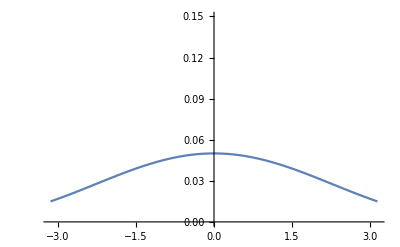

```mathematica
Plot[h[ξ,1],{ξ,-Pi,Pi},PlotRange->{0,0.15}]
```

```mathematica
h[Pi,1]
```

0.0149558

## Upper-bounding the Numerator

Let’s go back to the (ugly) numerator, and try to get an upper bound for that.

```mathematica
dFnum=Simplify[dFnum]
```

{0.06 Sin[ξ/2]-(4.16667 Sin[ξ/2])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2+(ⅇ^(20 t) t (800 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]-(400. Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (Cos[β0-ξ] (9.02778+1.67361 offset+(8.33333+2.16667 offset) Cos[ξ/2]+0.5 offset Cos[ξ])+4.16667 Sin[β0-ξ] Sin[ξ/2]) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2))/(160 √2 √(4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2)),(5 ⅇ^(20 t) t (-4 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (-Cos[β0]+(2 Cos[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]))/(4 √2 √(4 Abs[Cos[β0-ξ]]^2+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]^2))}

Note the presence of lowerBoundQty in the derivative for the “numerator”, as we would expect given the structure of that function. So let’s first get rid of that using the bound we just derived:

```mathematica
dFnum1=dFnum//.{Evaluate[lowerBoundQty[ξ,β0,offset]]->denLB}
```

{0.06 Sin[ξ/2]-(4.16667 Sin[ξ/2])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2+1/(160 √2 √denLB)ⅇ^(20 t) t (800 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]-(400. Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (Cos[β0-ξ] (9.02778+1.67361 offset+(8.33333+2.16667 offset) Cos[ξ/2]+0.5 offset Cos[ξ])+4.16667 Sin[β0-ξ] Sin[ξ/2]) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2),(5 ⅇ^(20 t) t (-4 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (-Cos[β0]+(2 Cos[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]))/(4 √2 √denLB)}

#### Deal with the first component:

SPLIT ON ADDITION

```mathematica
dFnum1Components=List@@dFnum1⟦1⟧
```

{0.06 Sin[ξ/2],-(4.16667 Sin[ξ/2])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2,1/(160 √2 √denLB)ⅇ^(20 t) t (800 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]-(400. Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (Cos[β0-ξ] (9.02778+1.67361 offset+(8.33333+2.16667 offset) Cos[ξ/2]+0.5 offset Cos[ξ])+4.16667 Sin[β0-ξ] Sin[ξ/2]) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2)}

The first two components are easily bounded as:

```mathematica
a1=dFnum1Components⟦1⟧/.Sin[ξ/2]->1
```

0.06

```mathematica
a2=Abs[dFnum1Components⟦2⟧/.{Sin[ξ/2]->1,Cos[ξ/2]->0}]
```

4.16667/Abs[8.33333+1.08333 offset]^2

Now we deal with the final component

SPLIT on PRODUCT

```mathematica
dFnum1Components⟦3⟧
```

1/(160 √2 √denLB)ⅇ^(20 t) t (800 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]-(400. Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (Cos[β0-ξ] (9.02778+1.67361 offset+(8.33333+2.16667 offset) Cos[ξ/2]+0.5 offset Cos[ξ])+4.16667 Sin[β0-ξ] Sin[ξ/2]) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2)

Capture the factor in front:

```mathematica
b3=Times@@((List@@dFnum1Components⟦3⟧)⟦;;-2⟧)
```

(ⅇ^(20 t) t)/(160 √2 √denLB)

Now split the

SPLIT ON ADDITION AGAIN

```mathematica
a3list=List@@Last[List@@dFnum1Components⟦3⟧]
```

{800 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]],-((400. Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (Cos[β0-ξ] (9.02778+1.67361 offset+(8.33333+2.16667 offset) Cos[ξ/2]+0.5 offset Cos[ξ])+4.16667 Sin[β0-ξ] Sin[ξ/2]) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2)}

```mathematica
Dimensions[a3list]
```

{2}

Now we will handle these terms manually:

```mathematica
a31=a3list⟦1⟧/.{Cos[β0-ξ]->1,Sin[β0-ξ]->1,Abs'->Sign}
```

800

```mathematica
a3list⟦2⟧
```

-((400. Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (Cos[β0-ξ] (9.02778+1.67361 offset+(8.33333+2.16667 offset) Cos[ξ/2]+0.5 offset Cos[ξ])+4.16667 Sin[β0-ξ] Sin[ξ/2]) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))])/(8.33333+1.08333 offset+1. offset Cos[ξ/2])^2)

```mathematica
a32=-a3list⟦2⟧/.{
Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]->(1+2/(offset+4/(0.52+0.48))),
Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]->1,
1/(8.333333333333334+1.0833333333333335 offset+1. offset Cos[ξ/2])^2->1/(8.333333333333334+1.0833333333333335 offset+1. offset *0)^2

}/.{
Cos[β0-ξ] ->1, Cos[ξ/2]->1, Cos[ξ]->1,Sin[β0-ξ] Sin[ξ/2]->1
}
```

(400. (21.5278+4.34028 offset) (1+2/(4.+offset)))/(8.33333+1.08333 offset)^2

```mathematica
comp1UB[denLB_,t_,offset_]:=Evaluate[(a1+a2+b3*a31+b3*a32)]
```

#### Deal with the second component:

```mathematica
dFnum1Components=List@@dFnum1⟦2⟧
```

{5/4,1/(√2),1/(√denLB),ⅇ^(20 t),t,-4 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]]+Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (-Cos[β0]+(2 Cos[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]}

```mathematica
b1=Times@@(dFnum1Components⟦;;-2⟧)
```

(5 ⅇ^(20 t) t)/(4 √2 √denLB)

```mathematica
a1List=List@@dFnum1Components⟦-1⟧
```

{-4 Abs[Cos[β0-ξ]] Sin[β0-ξ] Abs'[Cos[β0-ξ]],Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] (-Cos[β0]+(2 Cos[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))) Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]}

```mathematica
a1=-a1List⟦1⟧/.{
Cos[β0-ξ]->1, Sin[β0-ξ] ->1,Abs'->Sign
}
```

4

```mathematica
a2=a1List⟦2⟧/.{
Abs[Sin[β0]-(2 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))] ->(1+2/(offset+4/(0.52+0.48))),
(-Cos[β0]+(2 Cos[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))) ->(1+2/(offset+4/(0.52+0.48))),
Abs'[-10 Sin[β0]+(20 Sin[β0-ξ])/(offset+4/(0.52+0.48 Cos[ξ/2]))]->1
}
```

(1+2/(4.+offset))^2

```mathematica
comp2UB[denLB_,t_,offset_]:=Evaluate[b1*(a1+a2)]
```

## Combined bound for the Implicit Function Derivative on D\S_offset

It is now easy to assemble the above bounds into a single, overall bound for the derivative of the function t̃[ξ,β_0] outside the set S_offset (we will use the Max-norm here because it makes choosing the grid easier):

```mathematica
dBound[Toffset_,offset_]:=1/fullDenomLB[Toffset,offset]*Max[comp1UB[denomLB[Toffset,offset],Toffset,offset],comp2UB[denomLB[Toffset,offset],Toffset,offset]]
```

This gives us the following (somewhat reasonable) bound for the Lipschitz constant of the implicit function t̃[ξ,β_0] outside the set S_offset:

```mathematica
Tmax[offs]
```

0.25

```mathematica
offs
```

1

```mathematica
dBound[Tmax[offs],offs]
```

1.0633×10^9

```mathematica
1/fullDenomLB[Tmax[offs],offs]
```

2480.87

```mathematica
dBound[0.275,8]
```

8862.16

## Combining this code to create values for a Python lookup table

```mathematica
calcTable=(
Append[#,
"lut"->ParallelTable[
Quiet@Block[{ξ=Min[-Pi+(ξidx-1)*(2*Pi)/#"xiPoints",Pi],
β=Min[-betaMax+(βidx-1)*(2*betaMax)/#"betaPoints",betaMax]},
t/.Flatten@NSolve[Sqrt[2]*Lh*Norm[f[ξ, β, #"offs"]]*t*Exp[Lf*t] == h[ξ,  #"offs"],t]
],
{ξidx,1,#"xiPoints"+2},
{βidx,1,#"betaPoints"+2}
]
]
)&;
resultAssign[x_]:={"time"->x⟦1⟧,"lut"->x⟦2⟧};
calcTableFindMinimum=(
Append[#,
resultAssign@AbsoluteTiming[ParallelTable[
Block[{blkSize={Min[10*#"groupSize",#"xiPoints"+1-ξidx],Min[#"groupSize",#"betaPoints"+1-βidx]}},
Quiet[
{
N@Min[-Pi+(ξidx-1)*(2*Pi)/#"xiPoints",Pi],
N@Min[-betaMax+(βidx-1)*(2*betaMax)/#"betaPoints",betaMax],
Min[Table[
Block[
{ξ=Min[-Pi+(ξidx+xiInnerIdx-1)*(2*Pi)/#"xiPoints",Pi],
β=Min[-betaMax+(βidx+betaInnerIdx-1)*(2*betaMax)/#"betaPoints",betaMax]},
FindArgMin[(Sqrt[2]*Lh*Norm[f[ξ, β, #"offs"]]*t*Exp[Lf*t] - h[ξ,  #"offs"])^2,{t,0.2}]
],
{xiInnerIdx,0,blkSize⟦1⟧},
{betaInnerIdx,0,blkSize⟦2⟧}
]]-#"eps"
}
]
]
,
{ξidx,1,#"xiPoints"+1,10*#"groupSize"},
{βidx,1,#"betaPoints"+1,#"groupSize"}
]]
]
)&;
```

Compiled version using FindMinimum (no faster)

```mathematica
mainFun=Compile[{{blkSize,_Integer,1},{ξidx,_Integer},{βidx,_Integer},{xiPoints,_Integer},{betaPoints,_Integer},{offs,_Real},{eps,_Real}},
Module[{x},
x=Table[FindArgMin[(Sqrt[2]*Lh*Norm[f[Min[-Pi+(ξidx+xiInnerIdx-1)*(2*Pi)/xiPoints,Pi], Min[-betaMax+(βidx+betaInnerIdx-1)*(2*betaMax)/betaPoints,betaMax], offs]]*t*Exp[Lf*t] - h[Min[-Pi+(ξidx+xiInnerIdx-1)*(2*Pi)/xiPoints,Pi],  offs])^2,{t,0.2}],
{xiInnerIdx,0,blkSize⟦1⟧},
{betaInnerIdx,0,blkSize⟦2⟧}
];
{
N@Min[-Pi+(ξidx-1)*(2*Pi)/xiPoints,Pi],
N@Min[-betaMax+(βidx-1)*(2*betaMax)/betaPoints,betaMax],
Min[x]-eps
}
],
{{x,_Real,3},{FindArgMin[_],_Real,1}}
];
mainFunString="mainFun=Compile[{{blkSize,_Integer,1},{ξidx,_Integer},{βidx,_Integer},{xiPoints,_Integer},{betaPoints,_Integer},{offs,_Real},{eps,_Real}},
Module[{x},
x=Table[FindArgMin[(Sqrt[2]*Lh*Norm[f[Min[-Pi+(ξidx+xiInnerIdx-1)*(2*Pi)/xiPoints,Pi], Min[-betaMax+(βidx+betaInnerIdx-1)*(2*betaMax)/betaPoints,betaMax], offs]]*t*Exp[Lf*t] - h[Min[-Pi+(ξidx+xiInnerIdx-1)*(2*Pi)/xiPoints,Pi],  offs])^2,{t,0.2}],
{xiInnerIdx,0,blkSize⟦1⟧},
{betaInnerIdx,0,blkSize⟦2⟧}
];
{
N@Min[-Pi+(ξidx-1)*(2*Pi)/xiPoints,Pi],
N@Min[-betaMax+(βidx-1)*(2*betaMax)/betaPoints,betaMax],
Min[x]-eps
}
],
{{x,_Real,3},{FindArgMin[_],_Real,1}}
];";
ToExpression[mainFunString];
ParallelEvaluate[ToExpression[mainFunString];];
resultAssign[x_]:={"time"->x⟦1⟧,"lut"->x⟦2⟧};
calcTableFindMinimumCompiled=(
Append[#,
resultAssign@AbsoluteTiming[ParallelTable[
Block[{blkSize={Min[10*#"groupSize",#"xiPoints"+1-ξidx],Min[#"groupSize",#"betaPoints"+1-βidx]}},
mainFun[blkSize,ξidx,βidx,#"xiPoints",#"betaPoints",#"offs",#"eps"]
]
,
{ξidx,1,#"xiPoints"+1,10*#"groupSize"},
{βidx,1,#"betaPoints"+1,#"groupSize"}
]]
]
)&;
```

```mathematica
offsetList={1,2,4,6,8,16};
eps=0.01*ConstantArray[1,Length[offsetList]];
groupSize=10*ConstantArray[1,Length[offsetList]];
ToffsetInner={0.11,0.12,0.13,0.14,0.15,0.15};
ToffsetOuter=ToffsetInner-0.01;
chFact=500; (* Should be 1 :-( *)
xiGridPoints=Ceiling[(2*Pi)*(dBound@@@({ToffsetInner,offsetList}ᵀ))/eps/chFact];
betaGridPoints=Ceiling[(2*betaMax)*(dBound@@@({ToffsetInner,offsetList}ᵀ))/eps/chFact];
tableParams=Association@@@((Thread/@{"offs"->offsetList,"Tinner"->ToffsetInner,"Touter"->ToffsetOuter,"xiPoints"->xiGridPoints,"betaPoints"->betaGridPoints,"eps"->eps,"groupSize"->groupSize})ᵀ);
luts=Table[Null,{Length[tableParams]}];
SetDirectory[NotebookDirectory[]];
(*DumpSave["runcontext.mx",{Lh,f,Lf,h,vmax,lr,sigma,rBar,rmin,betaMax,tableParams,calcTable,calcTableFindMinimum,calcTableFindMinimumCompiled,mainFunString,resultAssign,chFact}];*)
(*luts=calcTable/@tableParams;*)
betaGridPoints*xiGridPoints
```

{96697910,49133785,32348925,59526012,158513327,48621171}

```mathematica
betaGridPoints*xiGridPoints
```

{96697910,49133785,32348925,59526012,158513327,48621171}

```mathematica
idx=-1;
AbsoluteTiming[luts⟦idx⟧=calcTableFindMinimum[tableParams⟦idx⟧];]
```

{20120.,Null}

```mathematica
luts⟦idx⟧["time"]/3600.
```

5.5889

```mathematica
Min[luts⟦idx⟧["lut"]⟦;;,;;,3⟧]
```

0.0182349

```mathematica
luts⟦idx⟧["lut"]
```

## Copy the LUT values (computed on a faster machine) to Python

### Setup Python (via custom Pythonika as usual)

```mathematica
pylink=Install["Pythonika"];
Py["import numpy as np"];
Py["import pickle"];
Py["import os"];
Py["os.chdir('"~~NotebookDirectory[]~~"')"];
```

### Import a luts variable computed elsewhere (same format as luts as above)

```mathematica
SetDirectory[NotebookDirectory[]];
<<"lut.mx";
```

```mathematica
luts⟦4⟧["lut"]//Dimensions
```

{201,297,3}

```mathematica
UnitConvert[Total[(Quantity[#["time"],"sec"])&/@luts],"hour"]
```

16.6907 h

Plot the output of a LUT at the same time as the Mathematica-computed numerical solution (i.e. on a different grid)

```mathematica
(* Compare the LUT with the original solution (WARNING: creates large, slow graphics) *)
ii=1;
numPoints=80;
offs=tableParams⟦ii⟧["offs"];
rng={{-Pi,Pi},{-betaMax,betaMax}};
data=Flatten[ParallelTable[
{xi,beta,t/.Flatten@Quiet@NSolve[Sqrt[2]*Lh*Norm[f[xi,beta,offs]]*t*Exp[Lf*t]==h[xi,offs],t]},
{xi,rng⟦1,1⟧,rng⟦1,2⟧,(rng⟦1,2⟧-rng⟦1,1⟧)/numPoints},
{beta,rng⟦2,1⟧,rng⟦2,2⟧,(rng⟦2,2⟧-rng⟦2,1⟧)/(2*numPoints)}
],1];
Show[
ListPlot3D[
data,
AxesLabel->(Style[#,FontSize->16]&/@{"ξ","β","Δt"}),
PlotRange->{0,0.19}
],
ListPlot3D[Flatten[luts⟦ii⟧["lut"],1],PlotTheme->"CoolColor"],
PlotRange->{0,0.15}
]
```

### Export these LUTs and associated information to a pickled Python dictionary

```mathematica
PyRealArray["x",luts⟦1⟧["lut"]⟦;;,;;,3⟧];
```

```mathematica
Py["xnp = np.array(x)"]
```

The following snippet transfers the LUT and associated information to a list of python dictionaries, and saves that list in a named pickle file.

```mathematica
pickleFile="energyShieldPyLUT.p";
Py["luts = []"];
(
ToPy["vmax",N[vmax]];
ToPy["rbar",N[rBar]];
ToPy["sigma",N[sigma]];
ToPy["lr",N[lr]];
ToPy["deltaFMax",N[deltaFMax]];
ToPy["betaMax",N[betaMax]];
ToPy["offs",#"offs"];
ToPy["Tinner",#"Tinner"];
ToPy["Touter",#"Touter"];
ToPy["numXiPoints",#"xiPoints"];
ToPy["numBetaPoints",#"betaPoints"];
ToPy["eps",#"eps"];
ToPy["groupSize",#"groupSize"];
ToPy["lutBuildTime",#"time"];
PyRealArray["lut",Clip[#"lut"⟦;;,;;,3⟧,{0.,N[#"Touter"]}]];
PyRealArray["xiPoints",#"lut"⟦;;,1,1⟧];
PyRealArray["betaPoints",#"lut"⟦1,;;,2⟧];
ToPy["xiIncrement",#"lut"⟦2,1,1⟧-#"lut"⟦1,1,1⟧];
ToPy["betaIncrement",#"lut"⟦1,2,2⟧-#"lut"⟦1,1,2⟧];
Py["\<
luts.append({ \
    'offs':offs, \
    'Tinner':Tinner, \
    'Touter':Touter, \
    'numXiPoints':numXiPoints, \
    'numBetaPoints':numBetaPoints, \
    'eps':eps, \
    'groupSize':groupSize, \
    'lutBuildTime':lutBuildTime, \
    'lut': np.array(lut, dtype=np.float64), \
    'xiPoints': np.array(xiPoints, dtype=np.float64), \
    'betaPoints': np.array(betaPoints, dtype=np.float64), \
    'xiIncrement': xiIncrement, \
    'betaIncrement': betaIncrement, \
    'vmax': vmax, \
    'rbar': rbar, \
    'sigma': sigma, \
    'lr': lr, \
    'deltaFMax': deltaFMax, \
    'betaMax': betaMax \
})
\>"];
)&/@luts;
Py["\<
with open('\>"~~pickleFile~~"\<','wb') as fp:
    pickle.dump(luts,fp)
\>"];
```

```mathematica
Py["vmax"]
```

20

```mathematica
deltaFMax
```

π/4